```mathematica
A=Import["C:\\Users\\Administrator\\Desktop\\CUMCM2017Problems\\支撑材料\\A题附件2.xls"][[2]]
```

{1}
 |  |  |  |

```mathematica
ListPlot3D[Table[Table[A[[r]][[c]],{r,1,512}],{c,1,180}],ColorFunction->Function[{x,y,z},RGBColor[100,120,z]]]
```

-Graphics3D-

```mathematica
Animate[ListPlot[Table[A[[r]][[c]],{r,1,512,1}],PlotStyle->{Blue},Joined->True],{c,1,180,1},AnimationRunning->TRUE]
```

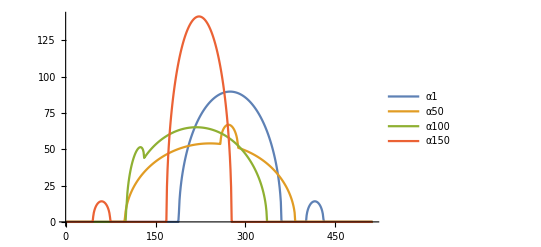

```mathematica
ListPlot[Table[A[[r]][[c]],{c,{1,50,100,150}},{r,1,512}],Joined->True,PlotLegends->{"α1","α50","α100","α150"}]
```

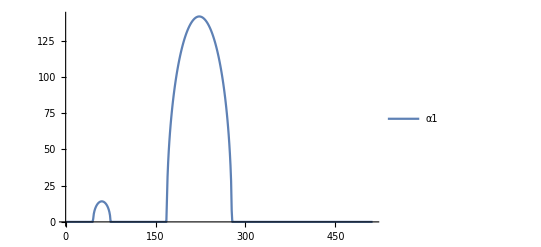

```mathematica
ListPlot[Table[A[[r]][[151]],{r,1,512}],{},Joined->True,PlotLegends->{"α1"}]
```

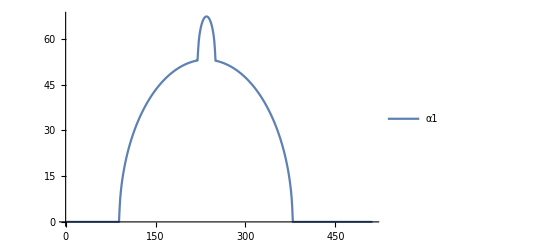

```mathematica
ListPlot[Table[A[[r]][[61]],{r,1,512}],{},Joined->True,PlotLegends->{"α1"}]
```